```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
loadTimeSeriesResampledShiftneg1=TimeSeriesShift[loadTimeSeriesResampled,{-1,"Hour"}]
```

TimeSeries[…]

```mathematica
DateListPlot[TimeSeriesWindow[loadTimeSeriesResampled,DateObject[{2019,1,1}],DateObject[{2019,1,2}]]]
```

DateListPlot::ldata: TimeSeriesWindow[«1»] is not a valid dataset or list of datasets.

DateListPlot[TimeSeriesWindow[TimeSeries[…],Day: Tue 1 Jan 2019,Day: Wed 2 Jan 2019]]

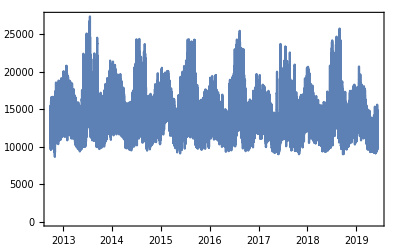

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
DateListPlot[loadTimeSeriesResampledShiftneg1]
```

-Graphics-

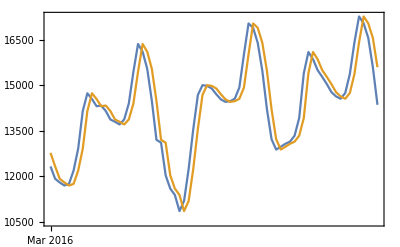

```mathematica
DateListPlot[{TimeSeriesWindow[loadTimeSeriesResampledShiftneg1,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}],TimeSeriesWindow[loadTimeSeriesResampled,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}]}]
```